```mathematica
Remove["Global`*"]
```

### Definitions of the γ-compounding algebra

```mathematica
γ=1/2;
Expγ[x_] := If[γ==0, Exp[x], (1+γ x)^(1/γ)];
Logγ[x_] := If[γ==0, Log[x], (x^γ-1)/γ];
Expη[x_, η_] := If[η==1, Exp[x], (1+(1-η) x)^(1/(1-η))];
Logη[x_, η_] := If[η==1, Log[x], (x^(1-η)-1)/(1-η)];
Clear[CircleTimes];
CircleTimes[x_,y_] := FullSimplify[PowerExpand[Expγ[Logγ[x] + Logγ[y]]]];
```

### Define parameters for simulations

```mathematica
X0 = 1;
T =100;
M = 50;
g = 3/2;
r = 1/2;
```

### Define analytical formulae

```mathematica
x2[t_, g_, r_] := (1/2^t Sum[Binomial[t,n]X0⊗Expγ[n Logγ[g+r]+(t-n)Logγ[g-r]], {n,0, t}]);
x3[X0_,t_, g_, r_] :=If[γ==0, X0(√(g^2-r^2))^t,X0 ⊗ Expγ[t/2(Logγ[g+r]+Logγ[g-r])]];
x4[X0_, t_, g_,r_] := 1/16((Logγ[g+r]-Logγ[g-r])^2 t + (4 √X0+(Logγ[g+r]+Logγ[g-r])t)^2);
```

### Generate some trajectories

```mathematica
X = Table[0,{i,1,T+1}, {j,1,M}];
B = Table[RandomInteger[{0,1}],{i,1,T}, {j,1,M}];
f[x_, b_, g_, r_] := If[b ==0, x ⊗ (g+r), x ⊗ (g-r)]
For[j=1, j<= M, j++, 
X[[1,j]]= X0;
For[i=2, i<= T+1, i++,
c = B[[i-1,j]];
X[[i,j]]= N[f[X[[i-1, j]], c, g, r]];
];

];
```

### Make some plots

Generate lin-lin plot for additive case, lin-log for the multiplicative case and log-log for the fractional case

```mathematica
SetOptions[{Plot,ListLogPlot, ListPlot, ListLogLogPlot},
Frame-> True,
LabelStyle->{FontFamily->"Arial", FontSize->12},
AspectRatio->1];
SetOptions[ListLogPlot,  Joined->True, FrameLabel->{"T", "X_T"}];
```

```mathematica
sampleTrajectories=TemporalData[X[[1;;T+1, 1;;M]],{Table[i-1, {i,1, T+1}]}];
F = Table[N[x2[t,g,r]],{t,0,T}];
expectedValue = TemporalData[F, {Table[i-1, {i,1, T+1}]}];
G = Table[N[x3[X0, t,g,r]],{t,0,T}];
typicalValue =  TemporalData[G, {Table[i-1, {i,1, T+1}]}];
```

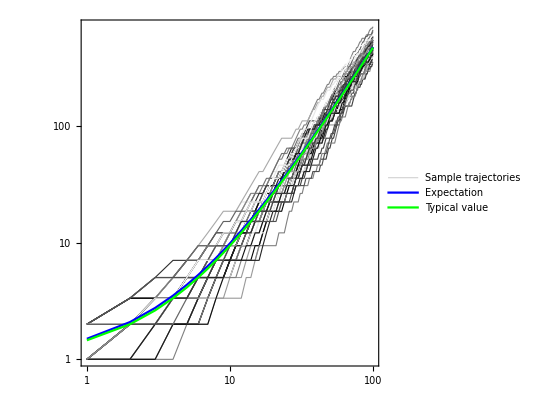

```mathematica
linestyles = Table[{GrayLevel[RandomReal[]], Thickness[0.002]}, {i,1,M}];
Switch[γ,
0
,
p1 = ListLogPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.26, 0.90}]];
p2 = ListLogPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.19, 0.85}]];
p3 = ListLogPlot[typicalValue,PlotStyle->{Green,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Typical value"}, {0.2, 0.80}]];
,
1
,
p1 = ListPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.25, 0.95}]];
p2 = ListPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.20, 0.85}]];
p3 = ListPlot[typicalValue,PlotStyle->{Green,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Typical value"}, {0.2, 0.75}]];
,
_
,
p1 = ListLogLogPlot[sampleTrajectories,PlotStyle->linestyles,PlotRange->All, Joined->True,  PlotLegends->Placed[{"Sample trajectories"}, {0.25, 0.95}]];
p2 = ListLogLogPlot[expectedValue,PlotStyle->{Blue,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Expectation"}, {0.20, 0.85}]];
p3 = ListLogLogPlot[typicalValue,PlotStyle->{Green,PointSize[.02]},PlotRange->All, Joined->True, PlotLegends->Placed[{"Typical value"}, {0.2, 0.75}]];
];
Show[p1,p2, p3, PlotRange->All]
```